# ASEN 5090

## Zach Dischner Homework 1

## Problem 1

How many sig figs must be included in degrees to fa fix accurate to 1cm?

1 minute is equal to 1852 meters

```mathematica
DegAccuracy = 1/(1852m/min*100cm/m*60.0min/deg)
```

(8.99928×10^-8 deg)/cm

By looking at the Exponent, to get down to the CM level, the degree measurement must have at least 8 sig figs

How many sig digits are required after decimal in the arc-second field if latitude is represented in deg, arc min, and arc-sec to describe fix accurate to 1cm?

```mathematica
ArcSecAccuracy=DegAccuracy*60min/deg * 60 sec/min
```

(0.000323974 sec)/cm

By looking at the Exponent, to get down to the CM level, the arc-sec measurement must have at least 4 sig figs

## Problem 2

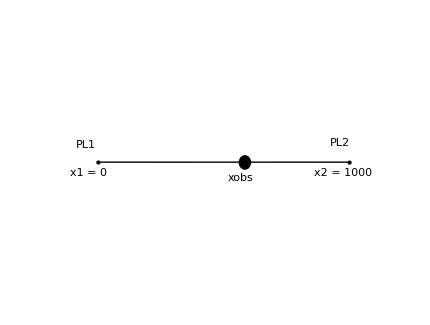
Observer is constrained to lie between two pseudolites, PL1 and PL2, separated by 1KM. Both have perfectly synchronized clocks, but observer may not. 

a. Given pseudoranges of 550m, 500m, find observer’s position and clock bias:
-Graphics-
ρ1  = √((x1-xobs)^2) - b
	turns into
ρ1  = |x1-xobs| - b
	which can be expressed in two forms 
ρ1  = x1-xobs - b 		or 		ρ1  = x1 + xobs - b
	Likewise, for pseudolite number 2
ρ2  = x2-xobs - b 		or 		ρ2  = x2 + xobs - b

Build 2 Equations, 2 unknowns using the absolute value equations

```mathematica
x1 = Quantity[0,"Kilometers"];
x2 = Quantity[1000,"Kilometers"];
rho1 = Quantity[500,"Kilometers"];
rho2 = Quantity[550, "Kilometers"];
sol=Solve[rho1==Abs[x1-Quantity[xobs,"Kilometers"]]-Quantity[b,"Kilometers"]&&rho2==Abs[x2-Quantity[xobs,"Kilometers"]]-Quantity[b,"Kilometers"],{xobs,b}]
```

{{xobs→475,b→-25}}

Observer position is at      475m. 	Clock Bias is at             -25m

```mathematica
b. Given pseudoranges of 400m 1400m find observer's position and clock bias:
```

Can rewrite in terms of 2 of the 4 expanded absolute value equations

```mathematica
rho1 = Quantity[400,"Kilometers"];
rho2 = Quantity[1400,"Kilometers"];
sol=Solve[rho1==x1-Quantity[xobs,"Kilometers"]-Quantity[b,"Kilometers"]&&rho2==x2+Quantity[xobs,"Kilometers"]-Quantity[b,"Kilometers"],{xobs,b}]
```

{{xobs→0,b→-400}}

Observer position is at      0m. 	Clock Bias is at             -400m

## Problem 3

Driving, set out from town A and go to B 120KM away. Odomoter is inaccurate, watch is accurate but has some bias. Don’t know what time it really is.

a. Odomoter says I’ve traveled 56KM. Estimate Position:

Estimated Position = 56 KM

b. Bus comes by, Exactly 21 minutes past the hour (leaving time) traveling at 3km/min. Can you estimate position?

Yes, you can estimate your position. The estimation will have a bias because your watch is not perfectly calibrated. But it is an ‘estimate’ after all.

c. Estimate position and clock bias given current information:

```mathematica
busTravelTime=21;
busSpeed = 3;
estFromOdometer=56;
estDistanceFromTime = busTravelTime * busSpeed;
(* Have two estimates for the position. 1 depends on time, so has a time bias. Solve this system of two equations, 2 unknowns*)
sol=Solve[X==estFromOdometer && 
		X==estDistanceFromTime-busSpeed*tBias,{X,tBias}]
```

{{X→56,tBias→7/3}}

Estimate for position  is 56 Km, and the clock bias is 2.333 minutes

d. Now, at 25 past the hour, blue bus drives by at 2.5 km/min, going from B to A. Bus leaves promptly on the hour and drives at a constant speed. Estimate position and clock bias based on all information so far:

```mathematica
(* Now, use both time measurements *)
bus2Speed = 2.5;
bus2TravelTime = 25;
difference = 120;
estDistanceFromTime2 = difference-bus2Speed*bus2TravelTime;

sol=Solve[X==busSpeed*busTravelTime -busSpeed*tBias && 
		X==difference-bus2Speed*(bus2TravelTime-tBias),{X,tBias}]
```

{{X→60.,tBias→1.}}

## Problem 4 Compute mean and STD of each column of data in data file and report why you chose the sig figs you did.

```mathematica
data=Import["/Users/zachdischner/Desktop/Dropbox/ASEN5090-GPS/Homework/1/HW1data.dat"]
```

{{0.64,35.0495},{0.23,35.0057},{0.03,35.4955},{0.95,35.2935},{0.95,35.3393},{0.47,35.4829},{0.,35.6245},{0.15,35.4717},{0.48,35.7321},{0.63,35.4567},{0.48,35.0233},{0.51,35.7177},{0.83,35.8106},{0.36,35.3045},{0.97,35.6869},{0.36,35.0497},{0.93,35.1555},{0.76,35.715},{0.77,35.9912},{0.58,35.3015},{0.22,35.5324},{0.44,35.9756},{0.51,35.2991},{0.23,35.2881},{0.5,35.4022},{0.4,35.8123},{0.99,35.7386},{0.4,35.5481},{0.6,35.6242},{0.64,35.6057},{0.15,35.3499},{0.64,35.6078},{0.74,35.9811},{0.21,35.3705},{0.,35.3342},{0.11,35.0754},{0.96,35.9829},{0.17,35.3148},{0.62,35.2739},{0.89,35.7777},{0.02,35.9086},{0.95,35.2198},{0.74,35.6107},{0.92,35.7388},{0.61,35.0868},{0.58,35.295},{0.45,35.1099},{0.1,35.1274},{0.18,35.8981},{0.27,35.2108},{0.61,35.1533},{0.2,35.7648},{0.59,35.4782},{0.86,35.521},{0.54,35.7101},{0.67,35.9466},{0.57,35.7073},{0.38,35.8111},{0.38,35.4244},{0.43,35.0319},{0.76,35.2876},{0.95,35.028},{0.39,35.7167},{0.38,35.7858},{0.05,35.9689},{0.62,35.5488},{0.2,35.371},{0.23,35.921},{0.72,35.7704},{0.73,35.3684},{0.04,35.1719},{0.19,35.9816},{0.97,35.9579},{0.73,35.2438},{0.06,35.6814},{0.76,35.6739},{0.27,35.9643},{0.07,35.448},{0.59,35.3081},{0.62,35.3242},{0.52,35.0885},{0.16,35.4216},{0.91,35.3046},{0.45,35.2163},{0.01,35.8429},{0.25,35.1781},{0.22,35.3168},{0.32,35.2184},{0.3,35.3783},{0.08,35.4404},{0.66,35.236},{0.53,35.0452},{0.94,35.101},{0.12,35.987},{0.87,35.3898},{0.98,35.4245},{0.45,35.3079},{0.29,35.1596},{0.04,35.9471},{0.12,35.8883}}

```mathematica
NumberForm[Mean[data[[All,1]]],2]
 NumberForm[StandardDeviation[data[[All,1]]],2]
```

0.5

0.3

The minimum number of sig figs in column 1’s data set is 2, so I am only reporting the stat to 2 sig figs

```mathematica
NumberForm[Mean[data[[All,2]]],6]
NumberForm[StandardDeviation[data[[All,2]]],4]
```

35.4877

0.2952

The minimum number of sig figs in column 2’s data set is 4, so I am only reporting the stat to 4 sig fig  for the standard deviation. And 6 sig figs for the average because of the leading two digits being important